Integrals for Line charge problem.  θ = 0,π/2,π are special cases, and have to be evaluated separately.  Also has a plot linechargeFig1.eps, and some plots (not in the book) of the integrands.

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

```mathematica
ClearAll[t, u, f]
$Assumptions =  t ∈ Reals ;
f[u_, t_] = (E^(I t) - u)((u^2 + 1 - 2 u Cos[t])^(-3/2));
f[u, θ]// TraditionalForm
ii = Integrate[ f[u, t], u] // FullSimplify;
ii // TraditionalForm
di = D[ii, u]// FullSimplify // TraditionalForm

iir = Integrate[ f[u, Pi/2], u] // FullSimplify;
iir// TraditionalForm
dir = D[iir, u]// FullSimplify // TraditionalForm
```

(-u+ⅇ^(ⅈ θ))/((u^2-2 u cos(θ)+1)^(3/2))

-(2 ⅇ^(2 ⅈ t) √(-2 u cos(t)+u^2+1))/((-1+ⅇ^(2 ⅈ t)) (-1+ⅇ^(ⅈ t) u))

ⅇ^(ⅈ t)/((1-ⅇ^(ⅈ t) u) √(-2 u cos(t)+u^2+1))

(1+ⅈ u)/(√(u^2+1))

-1/((u+ⅈ) √(u^2+1))

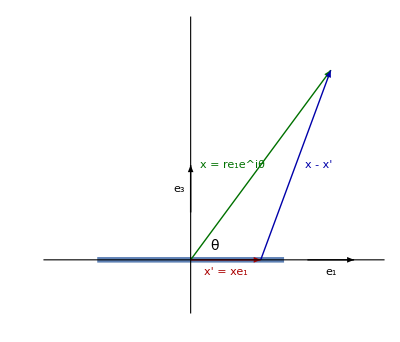

```mathematica
ClearAll[x,xp, o]
o = {0,0};
x = {3,4};
xp = {1.5,0};
e2 = {0,1};
e1 = {1,0};
bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;
tsub[t_,s_] := Subscript[bold[t]// fs,s];
esub := tsub[e, #]&;
vsub := tsub[v, #]&;
midpoint[p_] := (p[[1]] + p[[2]])/2 ;
midtext[p_, sh_,text_] := Text[text,midpoint[p] + sh]
p1 =Show[
ParametricPlot[{x,0}, {x,-2,2}, 
PlotStyle-> Thickness[0.01], GridLines -> Automatic,
Ticks->None,
PlotRange->{{-3,4}, {-1, 5}}
],
Graphics[ {
Green// Darker // Darker,
midtext[{o,x},-0.6 e1,Row[{ "x" // bold// fs, " = ", r// fs, esub[1], (e//fs)^("iθ" //fs)}]],
Arrow[{o,x}],
Red//Darker,
midtext[{o,xp},-e2/4,
Row[{ "x'" // bold// fs, " = ", "x"// fs, esub[1]}]],
 Arrow[{o,xp}],
Black,
Text["θ" // fs, 0.5(e1+0.6e2)],
Arrow[{e2,2e2}],
midtext[{e2,2e2},-0.25e1,esub[3]],
Arrow[{2.5e1,3.5e1}],
midtext[{2.5e1,3.5e1},-0.25e2,esub[1]],
Blue // Darker,
 Arrow[{xp,x}],
midtext[{xp,x},0.5e1, Row[{ "x" // bold// fs, " - ", "x'" // bold// fs}]]
}]
]
```

```mathematica
peeters`exportForLatex["linechargeFig1", p1]
```

{linechargeFig1.eps,linechargeFig1pn.png}

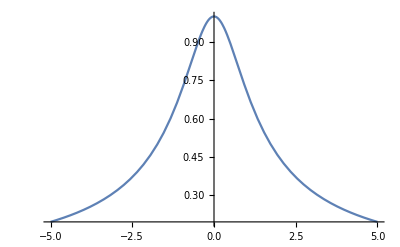

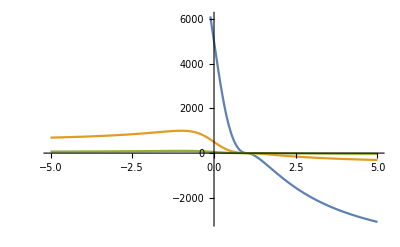

```mathematica
ClearAll[f,g, t]
f[u_] := (1 + I u)/Sqrt[1 + u^2];
g[u_, t_] := (1 - u E^(-I t)) Sqrt[1 + u^2 - 2 u Cos[t]]/(1 + u^2)/Sin[2 t];

Plot[ f[u] // Re, {u, -5, 5}]
Plot[((g[u, #] // Re) &/@ { 0.0001, 0.001, 0.01})// Evaluate,{u, -5, 5}]
```